```mathematica
Vivek Gupta|BSc(Hons) Computer Science|20211467|Practical 7

Find the Characteristics for the first order PDE and
Plotting them

Example 1:Find the Characteristics of the equation (u-y)u[(x,y),x]+y*u[(x,y),y]=x+y and plot them.
Solution:

The characteristics system is dx/(u-y)=dy/y=du/(x+y) using (i)+(ii)+(iii),we have v=(u+x)/y=c1,is a first integral.using (i)+(ii)=(iii),we have w=(x+y)^2-u*u=c2 is a second first integral.
```

```mathematica
f0=Plot3D[-x,{x,0,1},{y,0,1},PlotPoints->10];
f1=Plot3D[5 y-x,{x,0,1},{y,0,1},PlotPoints->10];
f2=Plot3D[10 y-x,{x,0,1},{y,0,1},PlotPoints->10];
g1=Show[f0,f1,f2];
h0=Plot3D[x+y,{x,0,1},{y,0,1},PlotPoints->10];
h1=Plot3D[Sqrt[(x+y)^2+5],{x,0,1},{y,0,1},PlotPoints->10];
h2=Plot3D[Sqrt[(x+y)^2+10],{x,0,1},{y,0,1},PlotPoints->10];
g2=Show[h0,h1,h2];
Show[GraphicsArray[{g1,g2}]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
Example 2:The solution of the equation u[(x,y),y]+u[x,y]*u[(x,y),x]  =  0can be interpreted as a vector field on the x-axis varying with time y.Find the integral satisfying the initial condition u(s,0)=h(s),where h is a given function.
Solution:

We plot the curves
{Ct:x=s+t(s^3-3s^2+4),u=s^3-3s^2+4_□}
```

```mathematica
u[s_]:=s^3-3 s^2+4;
x[s_,t_]:=s+t*u[s];
h0=ParametricPlot[{x[s,0],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0"]
h1=ParametricPlot[{x[s,0.2],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.2"]
h2=ParametricPlot[{x[s,0.3],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.3"]
h3=ParametricPlot[{x[s,0.33],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.33"]
h4=ParametricPlot[{x[s,0.333],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.333 "]
h5=ParametricPlot[{x[s,0.4],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.4"]
Show[GraphicsArray[{{h0,h1,h2},{h3,h4,h5}}].FrameTicks->None,Frame->False]
```

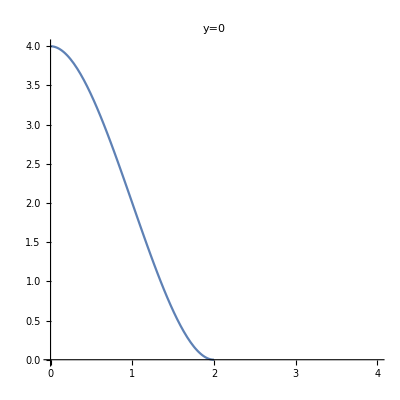
```mathematica
(-Graphics-_□)_□
```

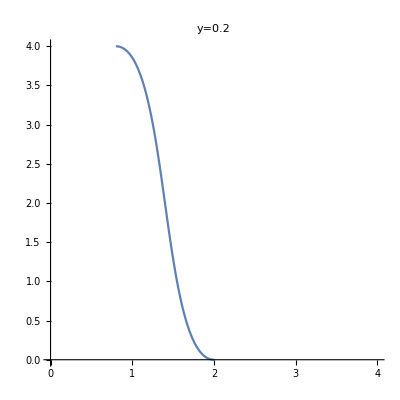
```mathematica
(-Graphics-_□)_(□_□)
```

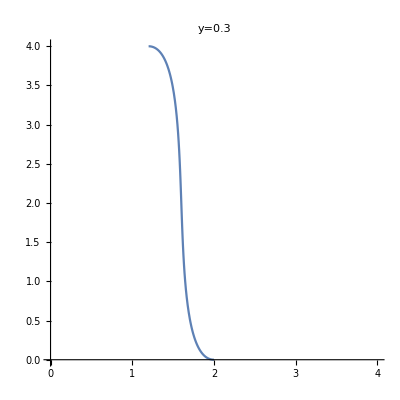
```mathematica
(-Graphics-_□)_□
```

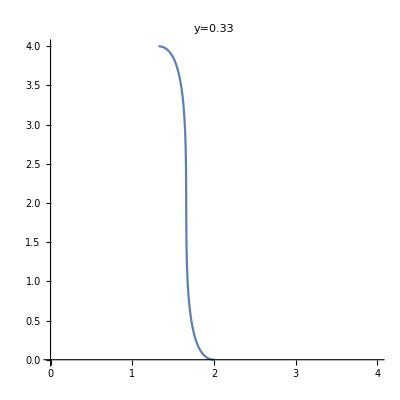
```mathematica
(-Graphics-_□)_□
```

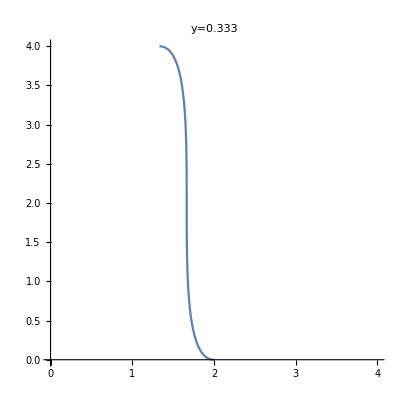
```mathematica
(-Graphics-_□)_□
```

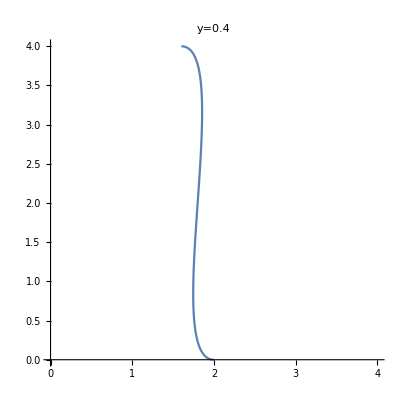
```mathematica
(□_□)_□-Graphics-_(((□_□)_□)_□)
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

Show::shx: No graphical objects to show.

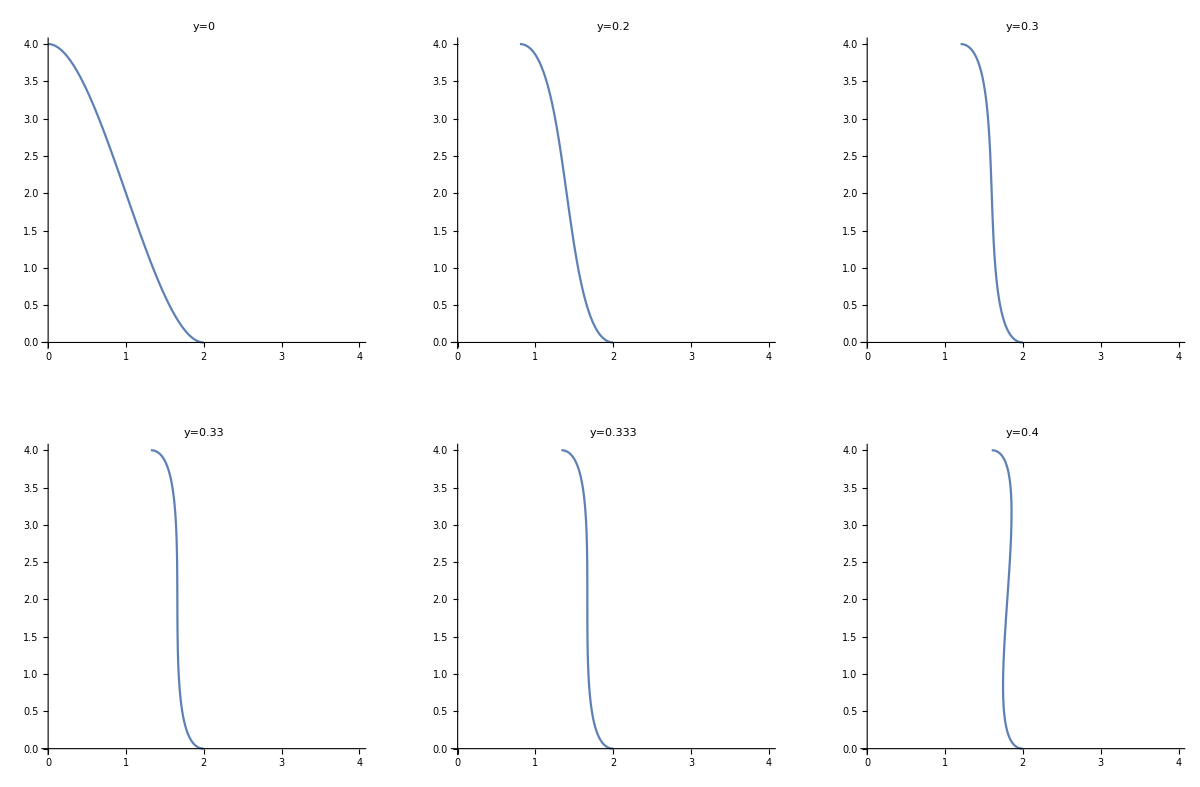
Show[-Graphics-.FrameTicks→None,Frame→False]